# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

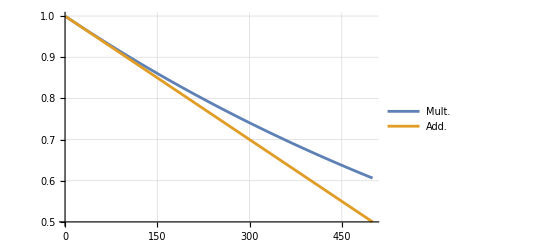

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params2={NN->1000,s->10^-3,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/1000,κ→1,L→2500,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(25 (1-ⅇ^(-2 B))^3)/((1+ⅇ^(-2 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-100]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.5]
```

0.359356

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.672323

```mathematica
getGammaHat[1,pbarExp02]
```

0.718712

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/1000,κ→1,L→2500,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-1.02344 (1-0.997098^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{999.991,547.861,400.585,368.803,361.555}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Exponential example

A function to generate an expression for the effective population size depending on time (t in generations) under the expansion scenario (corresponds to equation 5):

```mathematica
NeGenExp[anf_,end_,tchange_]:=Piecewise[{{anf(end/anf)^((tchange-t)/tchange),t<tchange},{anf,t≥tchange}}]
```

The resulting expression/the demographic scenario.

```mathematica
NGE=NeGenExp[2 1000,2 30000,850]
```

Piecewise[{{2^(4+(850-t)/850) 3^((850-t)/850) 5^(3+(850-t)/850), t<850}, {2000, t≥850}, {0, True}}]

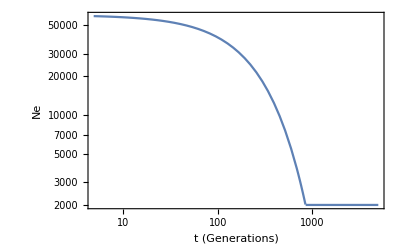

```mathematica
LogLogPlot[NGE,{t,0,5000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t (Generations)","Ne"}]
```

Equation 4 (distribution of time to coalescence, given the demographic scenario NGE - exponential increase):

```mathematica
qjtGenExp[j_,B_]:=Binomial[j,2]/(B NGE)Exp[-PiecewiseIntegrate[Binomial[j,2]/(B NGE/.t->σ),{σ,0,t}]]
```

Coalescence time for a pair of lineages under expansion model without BGS:

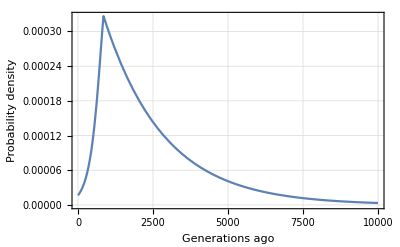

```mathematica
Plot[qjtGenExp[2,1],{t,0,10000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejGenExp[j_,B_]:=PiecewiseIntegrate[t qjtGenExp[j,B],{t,0,∞}]
```

Expected coalescence time for a pair of lineages under expansion model without BGS.

```mathematica
ejGenExp[2,1]//N
```

2596.63

Equation 8 (an expression for the probability to see b derived alleles in a sample of n with the effective population size scaled by B):

```mathematica
qnbGenExpL[n_,b_,B_]:=Sum[ejGenExp[j,B]wnbj[n,b,j],{j,2,n}]/Sum[ejGenExp[j,B]vnj[n,j],{j,2,n}]
```

As a test, derive an expression where B is set to 1 (no BGS). This does not have to be executed, and will be replicated in the last section (Including the effects of BGS - different values of B).

### Doing it on HRI

#### Smooth

An expression on Ne depending on τ

```mathematica
Nprime01
```

Piecewise[{{10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)), τ>0}, {0, True}}]

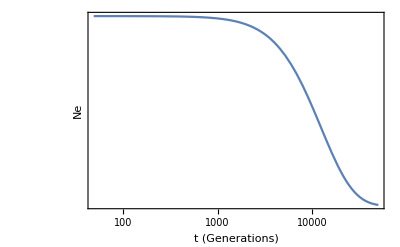

```mathematica
LogLogPlot[Nprime01,{τ,0,50000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t (Generations)","Ne"}]
```

Equation 4 (distribution of time to coalescence):

```mathematica
qjtHri01[j_]:=Binomial[j,2]/Nprime01 Exp[-Integrate[Binomial[j,2]/(Nprime01/.τ->σ),{σ,0,τ},Assumptions->{σ∈Reals,τ∈Reals}]]
```

Coalescence time for a pair of lineages under expansion model without BGS:

```mathematica
qjtHri01[2]/.τ-> 10000//AbsoluteTiming
```

{44.016,1/10000 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^10001)^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-Integrate[(ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000,{σ,0,10000},Assumptions→{σ∈ℝ,True}])}

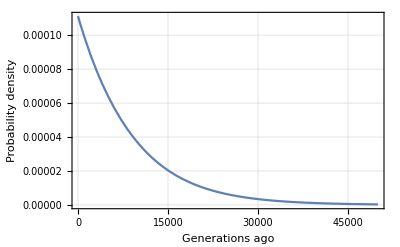

```mathematica
Plot[qjtHri01[2],{τ,0,50000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHri[j_]:=Integrate[τ qjtHri01[j],{τ,0,∞},Assumptions->{σ∈Reals,τ∈Reals}]
```

Expected coalescence time for a pair of lineages.

```mathematica
a01=(ejHri[2]//AbsoluteTiming)
```

{229.728,Integrate[1/10000 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-Integrate[(ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000,{σ,0,τ},Assumptions→{σ∈ℝ,τ∈ℝ}]) τ,{τ,0,∞},Assumptions→{σ∈ℝ,τ∈ℝ}]}

```mathematica
a01[[2]]
```

```mathematica
a02=(a01⟦2⟧//N//AbsoluteTiming)
```

NIntegrate::inumr: The integrand (ⅇ^(192/1811+«1»-Integrate[ⅇ^Plus[«2»]/10000,{σ,0,τ},Assumptions→{Element[«2»],Element[«2»]}]) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHri[n_,b_]:=Sum[ejHri[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHri[j]vnj[n,j],{j,2,n}]
```

```mathematica
Date[]
```

{2024,1,5,21,15,24.259001}

```mathematica
AbsoluteTiming[qnbHriL12b01=qnbHri[12,1]]
```

```mathematica
AbsoluteTiming[qnbHriL12b01s=qnbHriL12b01//Simplify]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

{3011.44,(3 (4522 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+16150 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+27132 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+29070 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/1000 ⅆσ) τ)/1000 ⅆτ+21945 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+12103 ∫_0^∞ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+4900 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+1428 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+285 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+35 ∫_0^∞ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+2 ∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ))/(149226 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+149226 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+48279 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+5775 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+209 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ)}

```mathematica
Hold[qnbHriL12b01]
```

Hold[qnbHriL12b01]

```mathematica
ByteCount[qnbHriL12b01]
```

$Aborted

```mathematica
SetAttributes[step,HoldAll]

step[expr_]:=Module[{P},P=(P=Return[#,TraceScan]&)&;
TraceScan[P,expr,TraceDepth->1]]
```

```mathematica
step[qnbHriL12b01s]
```

(3 (4522 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+16150 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+27132 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+29070 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/1000 ⅆσ) τ)/1000 ⅆτ+21945 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+12103 ∫_0^∞ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+4900 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+1428 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+285 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+35 ∫_0^∞ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+2 ∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ))/(149226 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+149226 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+48279 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+5775 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+209 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ)

```mathematica
ByteCount[qnbHriL12b01s]
```

```mathematica
AbsoluteTiming[N[qnbHriL12b01]]
```

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+«1»)^2 («1»)^3)/(10 (1+«1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
AbsoluteTiming[N[qnbHriL12b01s]]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+«1»)^2 («1»)^3)/(10 (1+«1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

{2024,1,5,22,21,42.499336}

```mathematica
AbsoluteTiming[qnbHriL12b11=qnbHri[12,11]//N]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

{2024,1,1,12,7,16.43248}

```mathematica
AbsoluteTiming[qnbHriL12=qnbHri[12,b];]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

{3841.83,Null}

```mathematica
Date[]
```

```mathematica
AbsoluteTiming[qnbHriL12b11//N]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+(«1»)^(«1»))^2 (1-«1»)^3)/(10 («1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
qnbHriL12/.b->2//N
```

$Aborted

```mathematica
(*AbsoluteTiming[qnbHriL12=Simplify[qnbHri[12,b], TimeConstraint->1];]*)
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

```mathematica
Table[qnbHriL12,{b,1,11}]//N
```

```mathematica
Date[]
```

$Aborted

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.02344 (1-0.997098^(1+τ))^2),999.991,359.356}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

{{x→0.,y→999.991},{x→500.,y→547.861},{x→1000.,y→400.585},{x→1500.,y→368.803},{x→2000.,y→361.555},{x→2500.,y→359.87},{x→3000.,y→359.476},{x→3500.,y→359.384},{x→4000.,y→359.363},{x→4500.,y→359.358},{x→5000.,y→359.357}}

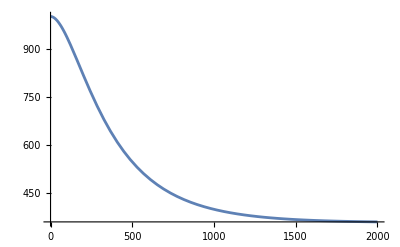

```mathematica
Plot[rAndL⟦1⟧,{τ,0,2000}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

rAndL

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→347.912},{τ→-170.656}}

```mathematica
inv
```

{{τ→-344.147 Log[5.03916×10^-17 (1.99023×10^16-1. √(3.96103×10^32-3.87031×10^32 Log[0.00278275425459248 y]))]},{τ→-344.147 Log[5.0391567298823×10^-17 (1.9902337196698×10^16+√(3.9610302589108×10^32-3.8703057397061×10^32 Log[0.00278275425459248 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-344.147 Log[5.03916×10^-17 (1.99023×10^16-1. √(3.96103×10^32-3.87031×10^32 Log[0.00278275425459248 y]))]

```mathematica
inv2/.y->660//N
```

347.912

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,108.491,216.981,325.472,433.962,542.453,650.944,759.434,867.925,976.415,1084.91}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.991,863.558,736.538,632.335,554.858,499.205,459.62,431.468,411.38,396.988,359.356}

```mathematica
xy1={xs,ys}//N
```

{{0.,108.491,216.981,325.472,433.962,542.453,650.944,759.434,867.925,976.415,1084.91},{999.991,863.558,736.538,632.335,554.858,499.205,459.62,431.468,411.38,396.988,359.356}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,66.6165,128.805,182.327,236.226,294.656,361.782,443.819,552.733,719.106,1084.91},{999.991,935.928,871.864,807.801,743.737,679.674,615.61,551.547,487.483,423.42,359.356}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-5.9477 0.997098^(1+τ) (1-0.997098^(1+τ)) ⅇ^(-1.02344 (1-0.997098^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

0.161653

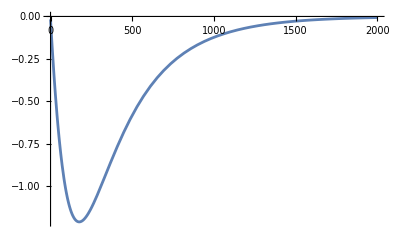

```mathematica
Plot[Nprime01p/.τ->t,{t,0,2000}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Piecewise[{{999.991, x<108.491}, {863.558, x<216.981}, {736.538, x<325.472}, {632.335, x<433.962}, {554.858, x<542.453}, {499.205, x<650.944}, {459.62, x<759.434}, {431.468, x<867.925}, {411.38, x<976.415}, {396.988, x<1084.91}, {359.356, x>1084.91}, {0., True}}]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{999.991, x<66.6165}, {935.928, x<128.805}, {871.864, x<182.327}, {807.801, x<236.226}, {743.737, x<294.656}, {679.674, x<361.782}, {615.61, x<443.819}, {551.547, x<552.733}, {487.483, x<719.106}, {423.42, x<1084.91}, {359.356, x>1084.91}, {0., True}}]

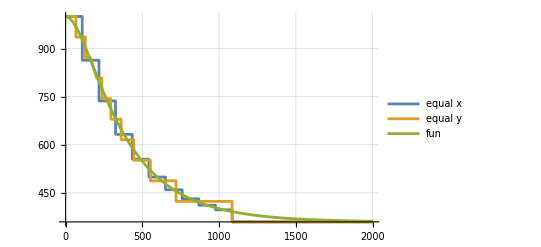

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,2000},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

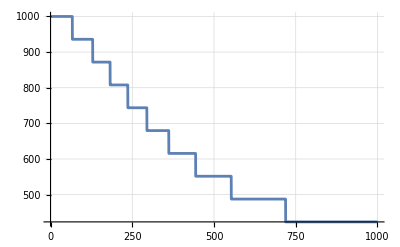

```mathematica
Plot[pwNe2/.x->t,{t,0,1000},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{999.991, x<66.6165}, {935.928, x<128.805}, {871.864, x<182.327}, {807.801, x<236.226}, {743.737, x<294.656}, {679.674, x<361.782}, {615.61, x<443.819}, {551.547, x<552.733}, {487.483, x<719.106}, {423.42, x<1084.91}, {359.356, x>1084.91}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

423.42

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

```mathematica
qjtHriPw01smooth[j_]:=Binomial[j,2]/np02 Exp[-Integrate[Binomial[j,2]/(np02/.τ->σ),{σ,0,τ},Assumptions->τ∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{1.20703,0.000862697}

```mathematica
qjtHriPw01smooth[2]/.τ-> 600//N//AbsoluteTiming
```

{3.46896,0.000846223}

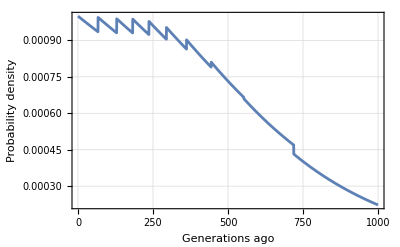

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

```mathematica
ejHriPwSmooth[j_]:=Integrate[τ qjtHriPw01smooth[j],{τ,0,∞}, Assumptions->τ∈Reals]
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{12.9598,599.115}

```mathematica
a01smooth=(ejHriPwSmooth[2]//AbsoluteTiming)
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

NIntegrate::nlim: σ = τ is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

NIntegrate::nlim: σ = τ is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: σ = τ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{31.2302,Integrate[(ⅇ^(1.02344 (1-0.997098^(1+τ))^2-Integrate[(ⅇ^(1.02344 (1-0.997098^(1+σ))^2))/1000,{σ,0,τ},Assumptions→τ∈ℝ&&τ>0]) τ)/1000,{τ,0,∞},Assumptions→τ∈ℝ]}

```mathematica
a01[[2]]
```

599.115

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
AbsoluteTiming[n12b1=qnbHriPw[12,1]]
```

{220.314,0.413224}

Equal x steps

{253.907,0.340639}

2 steps 30s, 3 steps 70s, 4 steps 263s, 5 steps 1334s (22min)
With Assumptions x ∈R:
5steps 206s, 6 steps 270, 7 steps 355, 8 steps 394s, 9 steps 435s

Duration similar irrespective of b.

```mathematica
n12All=AbsoluteTiming[n12b1=qnbHriPw[12,#]]&/@Range[1,11]
```

{{212.535,0.413224},{177.512,0.177479},{176.77,0.105818},{175.299,0.0728697},{174.444,0.0545042},{173.993,0.0430248},{173.701,0.035276},{173.393,0.0297467},{173.1,0.0256311},{175.457,0.0224646},{174.973,0.0199623}}

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{174.405,0.435723},{145.477,0.184826},{144.681,0.109549},{144.006,0.0752579},{142.8,0.0562673},{142.455,0.0444489},{141.802,0.0364934},{141.776,0.0308254},{141.513,0.0266096}}

```mathematica
Export["sfs10.txt", n10All]
```

sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{335.366,0.360495},{301.575,0.160202},{300.78,0.0973517},{300.003,0.0677397},{301.037,0.0509267},{301.384,0.0402702},{300.364,0.0330018},{300.533,0.0277762},{298.902,0.0238663},{298.986,0.0208479},{300.504,0.0184579},{300.564,0.0165256},{298.428,0.0149356},{298.215,0.0136076},{298.062,0.0124839},{298.067,0.0115224},{297.542,0.0106914},{297.707,0.00996697},{297.977,0.00933037}}

```mathematica
Export["sfs20.txt", n20All]
```

sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{690.693,0.304833},{623.161,0.141069},{622.787,0.0880718},{622.684,0.0624239},{622.817,0.0475338},{623.176,0.0379199},{623.621,0.0312601},{622.813,0.0264088},{622.994,0.0227385},{622.536,0.0198786},{622.167,0.0175965},{620.71,0.0157396},{620.431,0.0142037},{620.423,0.0129155},{621.37,0.0118219},{620.64,0.0108838},{620.362,0.0100715},{620.451,0.00936248},{620.599,0.00873897},{620.424,0.00818704},{621.924,0.00769554},{620.63,0.00725549},{620.187,0.00685953},{620.273,0.00650162},{620.931,0.00617676},{620.491,0.00588075},{620.321,0.00561005},{620.584,0.00536169},{620.562,0.00513311},{620.536,0.00492213},{620.482,0.00472686},{620.47,0.00454568},{620.657,0.00437717},{620.099,0.00422009},{620.359,0.00407336},{620.797,0.00393602},{620.367,0.00380723},{618.06,0.00368623},{618.464,0.00357237}}

```mathematica
Export["sfs40.txt", n40All]
```

sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1441.72,0.261063},{1321.75,0.124573},{1318.68,0.0796208},{1319.44,0.0574755},{1317.49,0.0444041},{1319.97,0.0358379},{1320.13,0.0298246},{1315.44,0.0253922},{1317.17,0.0220031},{1315.77,0.0193367},{1315.44,0.0171904},{1316.51,0.0154299},{1316.1,0.013963},{1315.06,0.0127244},{1313.84,0.0116664},{1312.99,0.0107537},{1313.22,0.00995939},{1312.68,0.00926276},{1313.66,0.00864755},{1312.47,0.00810088},{1312.83,0.00761238},{1313.48,0.00717364},{1313.07,0.00677776},{1316.55,0.00641904},{1313.55,0.00609271},{1313.1,0.00579477},{1313.52,0.00552185},{1313.02,0.00527107},{1313.29,0.00503996},{1316.72,0.0048264},{1315.21,0.00462857},{1314.11,0.00444486},{1313.49,0.00427389},{1313.45,0.00411443},{1312.96,0.00396542},{1312.44,0.00382591},{1312.89,0.00369506},{1312.47,0.00357212},{1313.2,0.00345644},{1312.89,0.00334742},{1313.04,0.00324452},{1314.33,0.00314726},{1313.1,0.00305522},{1311.98,0.00296801},{1312.64,0.00288527},{1312.77,0.00280667},{1312.49,0.00273194},{1312.92,0.00266081},{1314.3,0.00259303},{1313.9,0.00252838},{1312.79,0.00246666},{1312.69,0.00240768},{1313.16,0.00235127},{1312.77,0.00229727},{1312.56,0.00224555},{1312.97,0.00219595},{1312.77,0.00214837},{1308.22,0.00210268},{1302.04,0.00205879},{1305.87,0.00201658},{1312.32,0.00197597},{1312.35,0.00193687},{1312.18,0.0018992},{1312.51,0.00186289},{1312.51,0.00182787},{1312.9,0.00179407},{1312.46,0.00176144},{1313.84,0.00172991},{1314.26,0.00169944},{1313.64,0.00166997},{1313.44,0.00164145},{1312.77,0.00161385},{1311.87,0.00158711},{1312.56,0.00156121},{1313.5,0.0015361},{1312.8,0.00151175},{1311.83,0.00148813},{1312.78,0.0014652},{1311.33,0.00144294}}

```mathematica
Export["sfs80.txt", n80All]
```

sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11